```mathematica
Needs["ErrorBarPlots`"]
GenerateListOfFileNames[prefix_,date_,runtimes_]:=Module[{j,fileNames},
fileNames={};
For[j=1,j≤Length[runtimes],j++,
AppendTo[fileNames,StringJoin[prefix,date,"_",ToString[runtimes[[j]]],".dat"]]
];
fileNames
];
GetFileHeaderInfo[dataFileName_]:=Module[{rawFile,data,association,k},
rawFile=Import[dataFileName];
data={};
association=Association[];
k=1;
While[StringPart[rawFile[[k]][[1]],1]=="#",
association=Append[association,rawFile[[k]][[1]]->rawFile[[k]][[2]]];
k++;
];
association
];
(*ErrorListPlot2 is a convenience function. It accepts as an argument a list of lists. The first level of lists can have any length. The second level should have 3 elements. The first element is the independent variable, the second element is the dependent variable, and the third element is the error associated with the depenedent variable.*)
ErrorListPlot2[data_]:=Module[
{orderedPairs,dataT,errorValues,errorBars,errorBarData,i},
dataT=Transpose[data];
orderedPairs=Transpose[Drop[dataT,-1]];
errorValues=Drop[dataT,{1,2}];
errorBars=ErrorBar[errorValues][[1]];
errorBarData={};
For[i=1,i≤Length[data],i++,
AppendTo[errorBarData,{orderedPairs[[i]],ErrorBar[errorValues[[1]][[i]]]}];
];
ErrorListPlot[errorBarData]
];
GetFileDataset[dataFileName_]:=Module[{rawFile,headerStrippedData,columnHeaderLineNumber,lastColumnToImport,j,k,ass,tabularData,ds,rbAbsorptionRef,rbAbsorptionPro},
rawFile=Import[dataFileName];
k=1;

While[StringPart[rawFile[[k]][[1]],1]=="#",
k++;
];


headerStrippedData=Take[rawFile,{k,-1},All];
tabularData={};
For[j=2,j≤Length[headerStrippedData],j++,
If[Length[headerStrippedData[[j]]]>1,
ass=Association[];
For[k=1,k≤Length[headerStrippedData[[j]]],k++,
ass=Append[ass,headerStrippedData[[1]][[k]]->headerStrippedData[[j]][[k]]];
];
tabularData=Append[tabularData,ass];
]
];
ds =Dataset[tabularData]
];
ImportFile[dataFileName_]:={GetFileHeaderInfo[dataFileName],GetFileDataset[dataFileName]}
```

```mathematica
raspberryPi=FileNameJoin[{"Z:","RbData","2017-10-20"}];
dropBoxfolder=FileNameJoin[{"C:","Users","kahrendsen2","Dropbox"}];
dataFolder=FileNameJoin[{"00School","research","DataRuns"}];
folder=FileNameJoin[{dropBoxfolder,dataFolder}];
SetDirectory[folder];
FileNames[]

SetDirectory[FileNameJoin[{folder,"17-11-15_BalancedPhotoDetector"}]];
(*names=FileNames[StringExpression["POL",__,"_",__,DigitCharacter,".dat"]];*)
names=FileNames[]
```

{15-06-09_USBCounterError,15-07-06mockPolarizationData,16-01-14,16-01-21_Data,16-05-25_PolarizationData,16-07-06_PolarizationData,16-08-04_PolarizationData,16-08-07_HeliumTargetPictures,16-08-09_PolarizationData,16-10-17_polarimeter,16-10-27_DataReport,16-11-03_faradayRotation,16-11-07_faradayRotation,16-11-18_faradayRotation,16-12-09_faradayRotation,17-01-31,17-02-17_plusMinus,17-03-06_PlusMinusWavemeter,17-03-10_non-RbFaradayRotation,17-03-15_AimingFor5e12,17-03-15_wavemeterNoRb,17-03-28,17-03-29_pumpLaserFindingCircular,17-03-30_WavemeterReliability,17-04-04_polarization,17-04-06_polarization,17-04-07_wmReliability,17-04-18,17-04-18_polarization,17-04-22,17-04-25_ProbePolarizationDriftOpenChamber,17-04-30_laserReport,17-05-17_DirtyGunRun,17-05-18_ProbeDrift,17-05-19_BetterLaser,17-05-24_SimplifiedPolarization,17-05-25_LaserProfiling,17-06-02,17-06-06_IntensityOfProbeStudy,17-06-11,17-06-13,17-06-16,17-06-17,17-06-25,17-07-01_nRbVsBufferGasAnalysis,17-07-01_PumpLaserAnalysis,17-07-03_lowerNRb_BGPStudy,17-07-03_ProbeDrift,17-07-03_pumpBroadening,17-07-06_lotsOfProbeMeasurements,17-07-06_MagneticField,17-07-06_probePower,17-07-12_polVsPumpPower,17-08-01_rgaInitialScans,17-08-03_redoingSystemDiagnostic,17-08-06_probeDrift,17-08-18_furtherPolarizationStudy,17-08-19_furtherPolarizationStudy2,17-08-22_furtherPolarizationStudyFoundLeak,17-08-29_BvsProbePower_probeDetuneVsMagnetRot,17-09-05_Polarizations_100mTBGP,17-09-20,17-10-03_ElectronGun,17-10-16_ElectronGun,17-10-24_UnpolarizedPolarization,17-10-26_24And30eVRuns,17-10-28_24and30eVRedux,17-11-04_MoreUnpolarizedRuns,17-11-06_UnpolarizedRuns2,17-11-15_BalancedPhotoDetector,NewFile2.tsv,NewFile.tsv,pumpPower.png}

{FDayRotation2017-11-15_154904.dat,FDayRotation2017-11-15_222329.dat,FDayRotation2017-11-16_131648.dat,FDayRotation2017-11-16_135259.dat,intensityData1.csv,intensityData1.xlsx,intensityData2_steppingHWP.xlsx,intensityData3_every2degrees.xlsx,intensityData4_every10degreesFullRev.xlsx}

{{0,-0.632709},{10,-0.301737},{20,0.176707},{30,0.595536},{40,0.725605},{50,0.526762},{60,0.101978},{70,-0.365627},{80,-0.662784},{90,-0.631564},{100,-0.279983},{110,0.179455},{120,0.586529},{130,0.724994},{140,0.526151},{150,0.087552},{160,-0.390968},{170,-0.673394},{180,-0.627901},{190,-0.299752},{200,0.195637},{210,0.591185},{220,0.722628},{230,0.526151},{240,0.081216},{250,-0.378908},{260,-0.666753},{270,-0.629427},{280,-0.29357},{290,0.177622},{300,0.597216},{310,0.728276},{320,0.531189},{330,0.088086},{340,-0.376007},{350,-0.671028}}

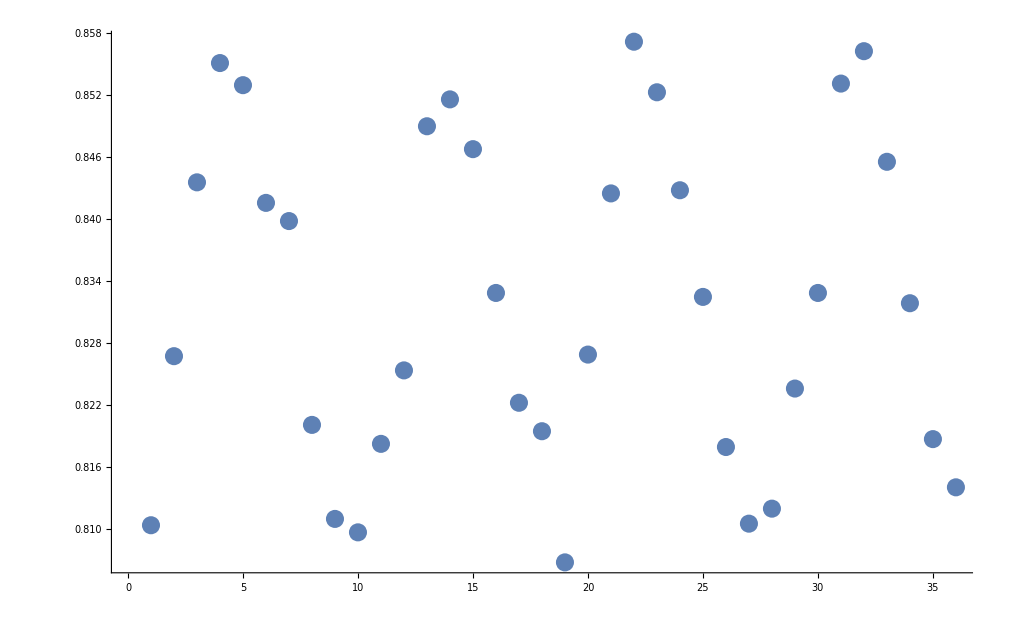

```mathematica
data=ImportFile[names[[2]]];
angle=Normal[data[[2]][All,"STEP"]];
det1=Normal[data[[2]][All,"PRB"]];
det2=Normal[data[[2]][All,"PUMP"]];
det3=Normal[data[[2]][All,"REF"]];
difference=det1-det2;
sum=det1+det2;
average=sum/2;
normalizedIntensity=difference/sum;

dataDet1=Transpose[{angle,det1}];
dataDet2=Transpose[{angle,det2}];
dataDiff=Transpose[{angle,difference}]
dataNorm=Transpose[{angle,normalizedIntensity}];
ListPlot[sum,LabelStyle->30]
```

```mathematica
DFTC[list_,rev_]:=Module[{numItems,i,k,j,returnList,intensity},
returnList={};
numItems=Length[list];

For[j=0,j<numItems/2,j++,
AppendTo[returnList,0];
];

For[k=1,k<=numItems,k++,
intensity=list[[k]];
For [i=0,i<numItems/2,i++,
If[i==0 ||i==(numItems/2-1),
returnList[[i+1]]=returnList[[i+1]]+1/numItems*intensity*Cos[2*π *i *rev* (k-1)/numItems];,
returnList[[i+1]]=returnList[[i+1]]+2/numItems*intensity*Cos[2*π *i* rev *(k-1)/numItems];
];
];
];

returnList
];
DFTS[list_,rev_]:=Module[{numItems,i,k,j,error,returnList,intensity,errors},
returnList={};
error={};
numItems=Length[list];

For[j=0,j<numItems/2,j++,
AppendTo[returnList,0];
AppendTo[errors,0];
];

For[i=1,i<=numItems,i++,
intensity=list[[i]];
For [k=0,k<numItems/2,k++,
If[k==0 ||k==(numItems/2-1),
returnList[[k+1]]=returnList[[k+1]]+1/numItems*intensity*Sin[2*π *k *rev* (i-1)/numItems];,
returnList[[k+1]]=returnList[[k+1]]+2/numItems*intensity*Sin[2*π *k* rev *(i-1)/numItems];
];
];
];

For[i=1,i<=numItems,i++,
intensity=list[[i]];
For [k=0,k<numItems/2,k++,
If[k==0 ||k==(numItems/2-1),
returnList[[k+1]]=returnList[[k+1]]+1/numItems*intensity*Sin[2*π *k *rev* (i-1)/numItems];,
returnList[[k+1]]=returnList[[k+1]]+2/numItems*intensity*Sin[2*π *k* rev *(i-1)/numItems];
];
];
];

returnList
];
DFT[list_,rev_]:={DFTS[list,rev],DFTC[list,rev]};
```

#### According to a Chp 22 in an optics handbook (chapter authored by Russell A. Chipman), We have the following mueller matrix for a general retarder

```mathematica
LR[θfast_,retardance_]:=({{1, 0, 0, 0}, {0, Cos[2θfast]^2+Sin[2θfast]^2Cos[2π retardance], Sin[2θfast]Cos[2θfast](1-Cos[2π retardance]), -Sin[2θfast]Sin[2π retardance]}, {0, Sin[2θfast]Cos[2θfast](1-Cos[2π retardance]), Sin[2θfast]^2+Cos[2θfast]Cos[2π retardance]^2, Cos[2 θfast]Sin[2π retardance]}, {0, Sin[2θfast]Sin[2π retardance], -Cos[2 θfast]Sin[2π retardance], Cos[2π retardance]}})
LRzero[δ_]:=({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, Cos[δ], Sin[δ]}, {0, 0, -Sin[δ], Cos[δ]}});
LPzero=1/2({{1, 1, 0, 0}, {1, 1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});
MuellerRotation[θ_]:=({{1, 0, 0, 0}, {0, Cos[2θ], -Sin[2θ], 0}, {0, Sin[2θ], Cos[2θ], 0}, {0, 0, 0, 1}})
```

#### We will assume our incident vector was 100% linearly polarized in the horizontal direction

```mathematica
inc=({{1}, {0}, {1}, {0}})
MatrixForm[(MuellerRotation[θ].LRzero[δ].Transpose[MuellerRotation[θ]])]
```

{{1},{0},{1},{0}}

(1 | 0 | 0 | 0
0 | Cos[2 θ]^2+Cos[δ] Sin[2 θ]^2 | Cos[2 θ] Sin[2 θ]-Cos[δ] Cos[2 θ] Sin[2 θ] | -Sin[δ] Sin[2 θ]
0 | Cos[2 θ] Sin[2 θ]-Cos[δ] Cos[2 θ] Sin[2 θ] | Cos[δ] Cos[2 θ]^2+Sin[2 θ]^2 | Cos[2 θ] Sin[δ]
0 | Sin[δ] Sin[2 θ] | -Cos[2 θ] Sin[δ] | Cos[δ])

## First, we pass the 45° light through a horizontal linear polarizer and a vertical linear polarizer.

### First Horizontal

```mathematica
LPzero.inc
```

{{1/2},{1/2},{0},{0}}

### Then vertical

```mathematica
vertLP=MuellerRotation[π/2].LPzero.Transpose[MuellerRotation[π/2]];
vertLP.inc
```

{{1/2},{-1/2},{0},{0}}

### Now we want to have an arbitrary linearly polarized input, and see how the intensity changes as the angle changes for both the vertical polarizer and the horizontal polarizer. We begin the arbitrary polarization at 45°.

```mathematica
arbinc=({{1}, {1}, {0}, {0}});
arbLP=MuellerRotation[θ].LPzero.Transpose[MuellerRotation[θ]];
arbinc=LR[θ,.5].arbinc;
LPzero.arbinc
vertLP.arbinc
balancedIntensity=(LPzero.arbinc)[[1]]-(vertLP.arbinc)[[1]]
```

{{1/2+1/2 (0.+Cos[2 θ]^2-1. Sin[2 θ]^2)},{1/2+1/2 (0.+Cos[2 θ]^2-1. Sin[2 θ]^2)},{0},{0}}

{{1/2+1/2 (0.-Cos[2 θ]^2+1. Sin[2 θ]^2)},{-1/2+1/2 (0.+Cos[2 θ]^2-1. Sin[2 θ]^2)},{0},{0}}

{0.+Cos[2 θ]^2-1. Sin[2 θ]^2}

### Looking at how the small angle approximation might be used to calculate the angle

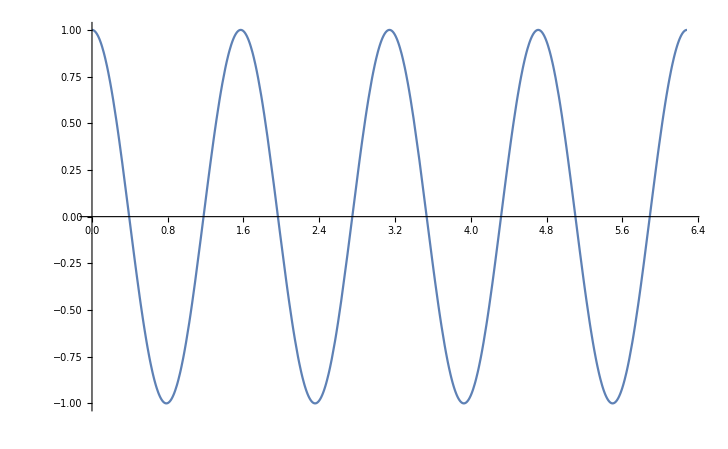

```mathematica
Plot[{balancedIntensity},{θ,0,2π}]
```

## Building a model for the rotating the HWP data

```mathematica
model1=A/2(1+Cos[2(θ+θo)*π/180]^2-Sin[2(θ+θo)*π/180]^2)+B
model2=A/2(1-Cos[2(θ+θo)*π/180]^2+Sin[2(θ+θo)*π/180]^2)+B
modelDifference=A*(Cos[2(θ+θo)*π/180]^2-Sin[2(θ+θo)*π/180]^2)

fit1=NonlinearModelFit[dataDet1,model1,{A,θo,B},θ]
fit2=NonlinearModelFit[dataDet2,model2,{A,θo,B},θ]
fitDiff=NonlinearModelFit[dataDiff,modelDifference,{A,θo},θ]
fitNorm=NonlinearModelFit[dataNorm,modelDifference,{A,θo},θ]
```

B+1/2 A (1+Cos[1/90 π (θ+θo)]^2-Sin[1/90 π (θ+θo)]^2)

B+1/2 A (1-Cos[1/90 π (θ+θo)]^2+Sin[1/90 π (θ+θo)]^2)

A (Cos[1/90 π (θ+θo)]^2-Sin[1/90 π (θ+θo)]^2)

FittedModel[0.789908-0.365714 (1+Cos[1/90 π (5.99716+θ)]^2-Sin[1/90 π (5.99716+θ)]^2)]

FittedModel[0.752051-0.3442 (1-Cos[1/90 π (5.96672+θ)]^2+Sin[1/90 π (5.96672+θ)]^2)]

FittedModel[-0.709914 (Cos[1/90 π (5.9824+θ)]^2-Sin[1/90 π (5.9824+θ)]^2)]

FittedModel[-0.852944 (Cos[1/90 π (5.96581+θ)]^2-Sin[1/90 π (5.96581+θ)]^2)]

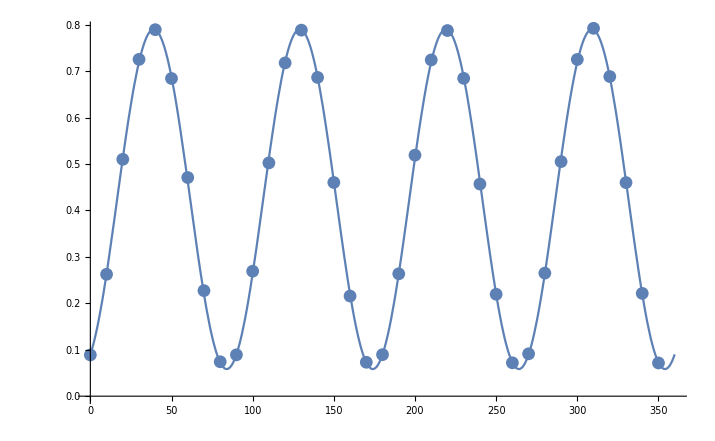

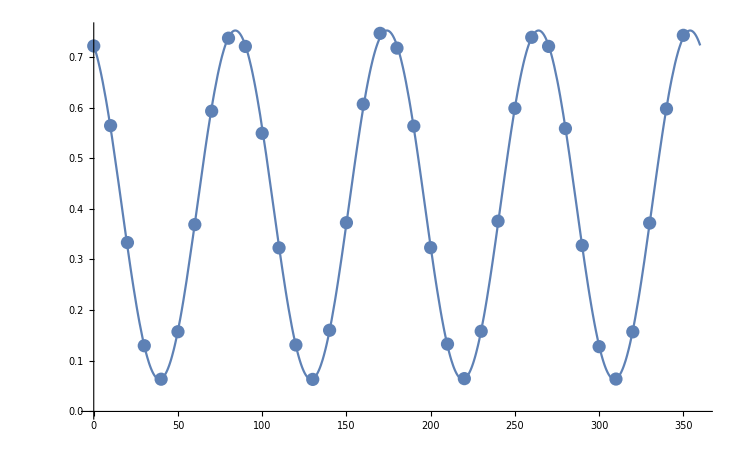

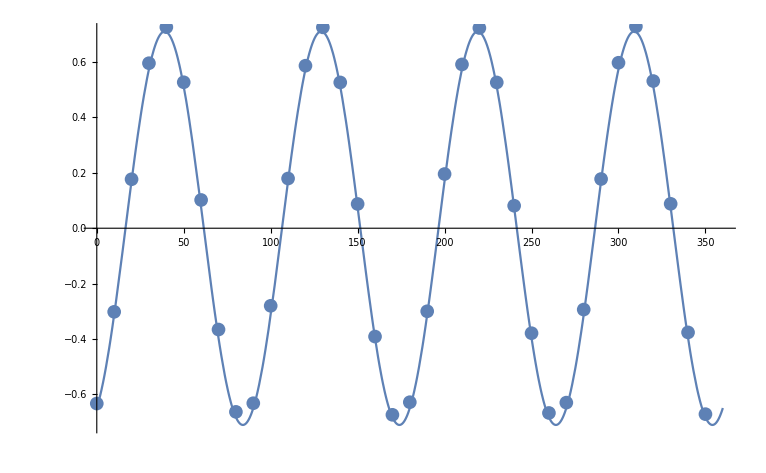

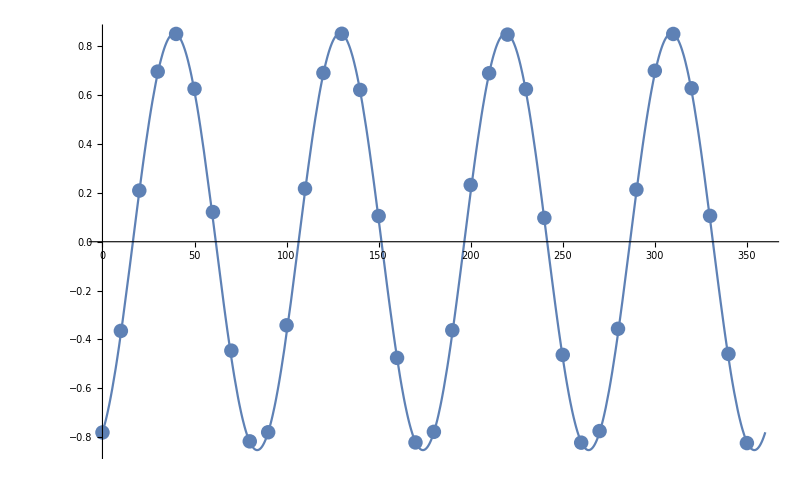

```mathematica
Show[{Plot[model1/.fit1["BestFitParameters"],{θ,0,360}],ListPlot[dataDet1]}]
Show[{Plot[model2/.fit2["BestFitParameters"],{θ,0,360}],ListPlot[dataDet2]}]
Show[{Plot[modelDifference/.fitDiff["BestFitParameters"],{θ,0,360}],ListPlot[dataDiff]}]
Show[{Plot[modelDifference/.fitNorm["BestFitParameters"],{θ,0,360}],ListPlot[dataNorm]}]
```

## Doing the same analysis at a different Probe Power

```mathematica
raspberryPi=FileNameJoin[{"Z:","RbData","2017-10-20"}];
dropBoxfolder=FileNameJoin[{"C:","Users","kahrendsen2","Dropbox"}];
dataFolder=FileNameJoin[{"00School","research","DataRuns"}];
folder=FileNameJoin[{dropBoxfolder,dataFolder}];
SetDirectory[folder];
FileNames[]

SetDirectory[FileNameJoin[{folder,"17-11-15_BalancedPhotoDetector"}]];
(*names=FileNames[StringExpression["POL",__,"_",__,DigitCharacter,".dat"]];*)
names=FileNames[]
```

{15-06-09_USBCounterError,15-07-06mockPolarizationData,16-01-14,16-01-21_Data,16-05-25_PolarizationData,16-07-06_PolarizationData,16-08-04_PolarizationData,16-08-07_HeliumTargetPictures,16-08-09_PolarizationData,16-10-17_polarimeter,16-10-27_DataReport,16-11-03_faradayRotation,16-11-07_faradayRotation,16-11-18_faradayRotation,16-12-09_faradayRotation,17-01-31,17-02-17_plusMinus,17-03-06_PlusMinusWavemeter,17-03-10_non-RbFaradayRotation,17-03-15_AimingFor5e12,17-03-15_wavemeterNoRb,17-03-28,17-03-29_pumpLaserFindingCircular,17-03-30_WavemeterReliability,17-04-04_polarization,17-04-06_polarization,17-04-07_wmReliability,17-04-18,17-04-18_polarization,17-04-22,17-04-25_ProbePolarizationDriftOpenChamber,17-04-30_laserReport,17-05-17_DirtyGunRun,17-05-18_ProbeDrift,17-05-19_BetterLaser,17-05-24_SimplifiedPolarization,17-05-25_LaserProfiling,17-06-02,17-06-06_IntensityOfProbeStudy,17-06-11,17-06-13,17-06-16,17-06-17,17-06-25,17-07-01_nRbVsBufferGasAnalysis,17-07-01_PumpLaserAnalysis,17-07-03_lowerNRb_BGPStudy,17-07-03_ProbeDrift,17-07-03_pumpBroadening,17-07-06_lotsOfProbeMeasurements,17-07-06_MagneticField,17-07-06_probePower,17-07-12_polVsPumpPower,17-08-01_rgaInitialScans,17-08-03_redoingSystemDiagnostic,17-08-06_probeDrift,17-08-18_furtherPolarizationStudy,17-08-19_furtherPolarizationStudy2,17-08-22_furtherPolarizationStudyFoundLeak,17-08-29_BvsProbePower_probeDetuneVsMagnetRot,17-09-05_Polarizations_100mTBGP,17-09-20,17-10-03_ElectronGun,17-10-16_ElectronGun,17-10-24_UnpolarizedPolarization,17-10-26_24And30eVRuns,17-10-28_24and30eVRedux,17-11-04_MoreUnpolarizedRuns,17-11-06_UnpolarizedRuns2,17-11-15_BalancedPhotoDetector,NewFile2.tsv,NewFile.tsv,pumpPower.png}

{FDayRotation2017-11-15_154904.dat,FDayRotation2017-11-15_222329.dat,FDayRotation2017-11-16_131648.dat,FDayRotation2017-11-16_135259.dat,intensityData1.csv,intensityData1.xlsx,intensityData2_steppingHWP.xlsx,intensityData3_every2degrees.xlsx,intensityData4_every10degreesFullRev.xlsx}

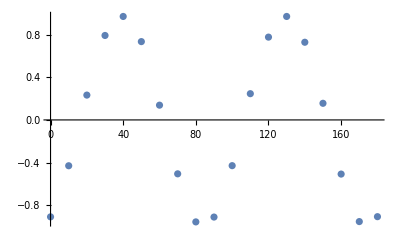

```mathematica
data=ImportFile[names[[3]]];
angle=Normal[data[[2]][All,"STEP"]];
det1=Normal[data[[2]][All,"PRB"]];
det2=Normal[data[[2]][All,"PUMP"]];
det3=Normal[data[[2]][All,"REF"]];
difference=det1-det2;
sum=det1+det2;
average=sum/2;
normalizedIntensity=difference/sum;

dataDet1=Transpose[{angle,det1}];
dataDet2=Transpose[{angle,det2}];
dataDiff=Transpose[{angle,difference}];
dataNorm=Transpose[{angle,normalizedIntensity}];
ListPlot[dataNorm]
```

```mathematica
fit1=NonlinearModelFit[dataDet1,model1,{A,θo,B},θ]
fit2=NonlinearModelFit[dataDet2,model2,{A,θo,B},θ]
fitDiff=NonlinearModelFit[dataDiff,modelDifference,{A,θo},θ]
fitNorm=NonlinearModelFit[dataNorm,modelDifference,{A,θo},θ]
```

FittedModel[0.492468-0.245199 (1+Cos[1/90 π (5.71252+θ)]^2-Sin[1/90 π (5.71252+θ)]^2)]

FittedModel[0.463424-0.228358 (1-Cos[1/90 π (5.68098+θ)]^2+Sin[1/90 π (5.68098+θ)]^2)]

FittedModel[-0.472431 (Cos[1/90 π (5.71165+θ)]^2-Sin[1/90 π (5.71165+θ)]^2)]

FittedModel[-0.983121 (Cos[1/90 π (5.67105+θ)]^2-Sin[1/90 π (5.67105+θ)]^2)]

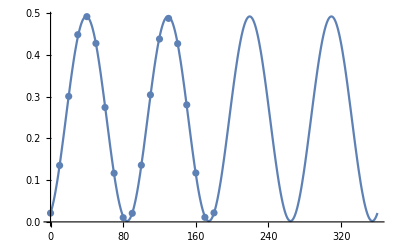

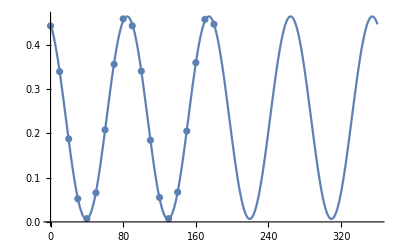

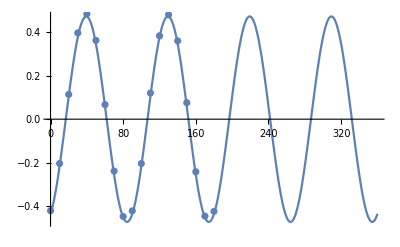

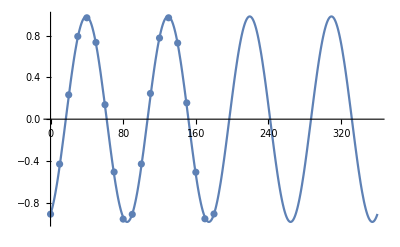

```mathematica
Show[{Plot[model1/.fit1["BestFitParameters"],{θ,0,360}],ListPlot[dataDet1]}]
Show[{Plot[model2/.fit2["BestFitParameters"],{θ,0,360}],ListPlot[dataDet2]}]
Show[{Plot[modelDifference/.fitDiff["BestFitParameters"],{θ,0,360}],ListPlot[dataDiff]}]
Show[{Plot[modelDifference/.fitNorm["BestFitParameters"],{θ,0,360}],ListPlot[dataNorm]}]
```

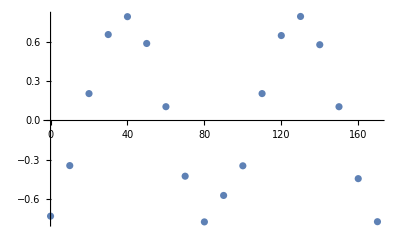

```mathematica
data=ImportFile[names[[4]]];
angle=Normal[data[[2]][All,"STEP"]];
det1=Normal[data[[2]][All,"PRB"]];
det2=Normal[data[[2]][All,"PUMP"]];
det3=Normal[data[[2]][All,"REF"]];
difference=det1-det2;
sum=det1+det2;
average=sum/2;
normalizedIntensity=difference/sum;

dataDet1=Transpose[{angle,det1}];
dataDet2=Transpose[{angle,det2}];
dataDiff=Transpose[{angle,difference}];
dataNorm=Transpose[{angle,normalizedIntensity}];
ListPlot[dataNorm]
```

FittedModel[0.529326-0.232011 (1+Cos[1/90 π (5.9694+θ)]^2-Sin[1/90 π (5.9694+θ)]^2)]

FittedModel[0.507935-0.223126 (1-Cos[1/90 π (6.0235+θ)]^2+Sin[1/90 π (6.0235+θ)]^2)]

FittedModel[-0.455137 (Cos[1/90 π (5.99592+θ)]^2-Sin[1/90 π (5.99592+θ)]^2)]

FittedModel[-0.781638 (Cos[1/90 π (6.0645+θ)]^2-Sin[1/90 π (6.0645+θ)]^2)]

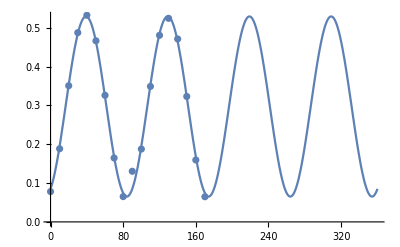

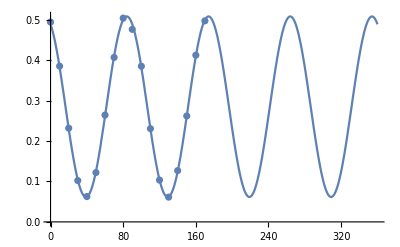

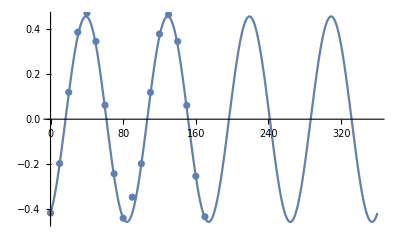

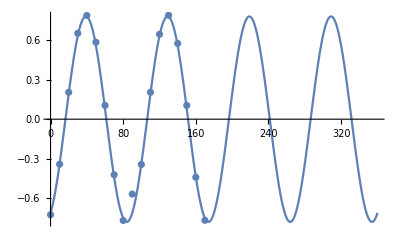

```mathematica
fit1=NonlinearModelFit[dataDet1,model1,{A,θo,B},θ]
fit2=NonlinearModelFit[dataDet2,model2,{A,θo,B},θ]
fitDiff=NonlinearModelFit[dataDiff,modelDifference,{A,θo},θ]
fitNorm=NonlinearModelFit[dataNorm,modelDifference,{A,θo},θ]
Show[{Plot[model1/.fit1["BestFitParameters"],{θ,0,360}],ListPlot[dataDet1]}]
Show[{Plot[model2/.fit2["BestFitParameters"],{θ,0,360}],ListPlot[dataDet2]}]
Show[{Plot[modelDifference/.fitDiff["BestFitParameters"],{θ,0,360}],ListPlot[dataDiff]}]
Show[{Plot[modelDifference/.fitNorm["BestFitParameters"],{θ,0,360}],ListPlot[dataNorm]}]
```